# Doing The Elliptic Integrals

```mathematica
Clear[k,D1P,D2P,D1M,D2M,J,A,ϛP,ϡP,ϟP,RP,p2,e,b,d,c,f,B,p2,βP, αP ,ϛP,ϡP,γP,ωP ,φP,k,B,βM, αPM,ϛM,ϡM,γM,ωM,φM,Þ,ð,ϵ,RM,RP,L,a,KZ,Z2,Z1]
```

```mathematica
Clear["Global`*"]
```

## Constants

```mathematica
ClearAll;
M = 1`50;
a = 0.62`50;
ϵ = 0.9`50(*COM["ℰ"];*);
L =0.3`50(*COM["ℒ"];*);
Q = 5`50(*COM["𝒬"];*);

J = 1-ϵ^2;
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];

ROOTS = r/.Solve[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)==0,r];

ReallRoots = Select[ROOTS,Im[#]==0&];
ComplexRoots = Select[ROOTS,Im[#]!=0&];

R1= ReallRoots[[1]]
R2= ReallRoots[[2]]
R3=ComplexRoots[[1]]
R4= ComplexRoots[[2]]
Z1=Sqrt[1/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);

R[r_] := -J(r-R1)(r-R2)(r-R3)(r-R4);
hR = (R3-R4)/(R3-R1);
hP = hR(R1-RP)/(R4-RP);
hM =  hR(R1-RM)/(R4-RM);
e = R2;
b = R1;
c = Re[R3];
d = -Im[R4];
A = Sqrt[(e-c)^2+d^2];
B  = Sqrt[(b-c)^2+d^2];
chi = (A*b+e*B)/(A+B);
k = Sqrt[((e-b)^2-(A-B)^2)/(4*A*B)];
p2 = b*A^2+e*B^2-(e+b)*A*B;
f = (4 A B)/(A-B)^2;
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


Þ = Evaluate[4A B( p2(b+e) -A B (b-e)^2)];
ð = Evaluate[8 A^2 B^2(b^2+e^2)];
χ = Evaluate[8 A^2 B^2(b^2-e^2)] ;
ψ = Evaluate[4 A B (b-e) p2];


ϡM =(p2-(A-B)^2 RM)^2 ;
ϛM = 4 A B (A^2 RM (-b-e+2 RM)+(b+e-2 RM) (p2-B^2 RM)+A B ((b-e)^2+2 (b+e) RM-4 RM^2));
ϟM =16 A^2 B^2 (-b+RM) (-e+RM);
αM =-(A^2 (A-B)^2 RM-2 A (A-B)^2 B RM+(A-B)^2 (-p2+B^2 RM)) ;
βM = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RM+4 A (A-B)^2 B RM-8 A^2 B^2 RM+4 A B (-p2+B^2 RM));
γM= -(2 A b (A-B)^2 B-2 A (A-B)^2 B  e);
φM = 8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RM;
ωM = -8 A^2 b B^2 +8 A^2 B^2 e;


ϡP =(p2-(A-B)^2 RP)^2 ;
ϛP = 4 A B (A^2 RP (-b-e+2 RP)+(b+e-2 RP) (p2-B^2 RP)+A B ((b-e)^2+2 (b+e) RP-4 RP^2));
ϟP =16 A^2 B^2 (-b+RP) (-e+RP);
αP =-(A^2 (A-B)^2 RP-2 A (A-B)^2 B RP+(A-B)^2 (-p2+B^2 RP)) ;
βP = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RP+4 A (A-B)^2 B RP-8 A^2 B^2 RP+4 A B (-p2+B^2 RP));
γP= -(2 A b (A-B)^2 B-2 A (A-B)^2 B  e);
φP = 8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RP;
ωP = -8 A^2 b B^2 +8 A^2 B^2 e;


DENOMROOTSM =Solve[ϡM λ^4+ϛM  λ^2 +ϟM==0,λ];

D1M=Sqrt[ -f];
D2M=Sqrt[(4 A B (RM-b) (e-RM))/(A( b-RM)-B( e- RM))^2];

DENOMROOTSP =Solve[ϡP λ^4+ϛP λ^2 +ϟP==0,λ];

D1P=Sqrt[ -f];
D2P=Sqrt[(4 A B (RP-b) (e-RP))/(A( b-RP)-B( e- RP))^2];

AMR[λ_]:= JacobiAmplitude[√(A B J) λ,k^2];
SNR[λ_]:= JacobiSN[√(A B J) λ,k^2];
CNR[λ_]:= JacobiCN[√(A B J) λ,k^2];
DNR[λ_]:= JacobiDN[√(A B J) λ,k^2];


AMZ[λ_] := JacobiAmplitude[Z2 λ,KZ]



xSUB[r_] := (2Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b));
```

0.210435560436072256970283133057223722097325314803

7.92664839031059661406147913427830496759658921433

1.1946159193635076697472767610690777604162006302-2.15344787341151056720366278501584757160449034148 ⅈ

1.1946159193635076697472767610690777604162006302+2.15344787341151056720366278501584757160449034148 ⅈ

#### Practice Integrals

```mathematica
qR0 = 0;
Subscript[Υ, r] = π/(2*EllipticK[KR])Sqrt[J(R3-R1)(R4-R2)];
qR[λ_]:= (Subscript[Υ, r] λ+ qR0);
r1[λ_]:=(R1(R3-R4)(JacobiSN[EllipticK[KR]/π* (Subscript[Υ, r]*λ+ qR0),KR])^2-R4(R3-R1))/((R3-R4)(JacobiSN[EllipticK[KR]/π* (Subscript[Υ, r]*λ+qR0),KR])^2-(R3-R1));
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);

Plot[{Re@r1[λ]},{λ,-1,1},PlotLegends->{SOlMaarten}];

Plot[{Re@(r1'[λ])^2,Re[RPoly1[r1[λ]]],Re[(r1'[λ])^2-RPoly1[r1[λ]]]},{λ,-3,3},PlotLegends->{Sol1PRIME,POLY,Diff}];

Clear[CI,a,b,c,d,R1,R2,R3,R4,KR,Υ,qR0,J,p2]
FullSimplify[Solve[r==(R3(R1-R2)(JacobiSN[ 1/2 Sqrt[J(R1-R3)(R2-R4)]λ,KR])^2-R2(R1-R3))/((R1-R2)(JacobiSN[ 1/2 Sqrt[J(R1-R3)(R2-R4)]λ,KR])^2-(R1-R3)),λ]];
Solve::ifun: "Inverse functions are being used by \!\(\*RowBox[{\"Solve\"}]\), so some solutions may not be found; use Reduce for complete solution information."
FullSimplify[((2 (a-b) (a-c) (b-c) x)/((-a+c+(a-b) x^2)^2))/Sqrt[((-c(a-b)x^2+b(a-c))/(-(a-b)x^2+(a-c))-a)((-c(a-b)x^2+b(a-c))/(-(a-b)x^2+(a-c))-b)((-c(a-b)x^2+b(a-c))/(-(a-b)x^2+(a-c))-c)((-c(a-b)x^2+b(a-c))/(-(a-b)x^2+(a-c))-d)]]
(0.3522163848991588 (-24.381664131162402+b) (-0.99+b) x)/((-23.391664131162404+(-0.99+b) x^2)^2 √(-((1. (-24.381664131162402+1. b) (24.137847489850778+(-25.3716641311624+b) b) x^2 (0.99-0.9899999999999999 x^2+b (-1.+1. x^2)) (-41.0798618032598-0.99 x^2+b (0.7254713040481092+1. x^2)))/(-23.391664131162404+(-0.99+b) x^2)^4)))
2/(Sqrt[J(a-c) (b-d)] √((-1+x^2) (1-((a-b) (c-d))/((a-c) (b-d)) x^2)))
CPractise = 2/Sqrt[J(a-c) (b-d)]

MINOCOM[r_]:=2/Sqrt[J*4*A*B] InverseJacobiSN[2*Sqrt[A*B] Sqrt[(e-r)(r-b)]/(B(e-r)+A(r-b)),KZ2];
CI = 1/Sqrt[J*A*B];
FullSimplify[Solve[λ==2/Sqrt[J*4*A*B] InverseJacobiSN[2*Sqrt[A*B] Sqrt[(e-r)(r-b)]/(B(e-r)+A(r-b)),KZ2],r]];

rSOLCom[λ_]:= ((A-B) (A b-B e) JacobiSN[√(A B J) λ,KZ2]^2+2 A B ((b+e)+(b-e) JacobiCN[√(A B J) λ,KZ2]))/(4 A B+(A-B)^2 JacobiSN[√(A B J) λ,KZ2]^2);
Plot[{(rSOLCom'[λ])^2, RPoly1[rSOLCom[λ]],(rSOLCom'[λ])^2- RPoly1[rSOLCom[λ]]},{λ,-1.5,1.5},PlotLegends->{SOLPRIME,POLY,diff},PlotRange->{{-1.5,1.5},{-1,1}}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse functions are being used by `1`, so some solutions may not be found; use Reduce for complete solution information.

(2 (a-b) (a-c) (b-c) x)/((-a+c+(a-b) x^2)^2 √(((a-b)^2 (a-c)^2 (b-c)^2 x^2 (-1+x^2) ((a-c) (b-d)-(a-b) (c-d) x^2))/((-a+c+(a-b) x^2)^4)))

(0.352216 (-24.3817+b) (-0.99+b) x)/((-23.3917+(-0.99+b) x^2)^2 √(-(1. (-24.3817+1. b) (24.1378+(-25.3717+b) b) x^2 (0.99-0.99 x^2+b (-1.+1. x^2)) (-41.0799-0.99 x^2+b (0.725471+1. x^2)))/((-23.3917+(-0.99+b) x^2)^4)))

2/(√((a-c) (b-d) J) √((-1+x^2) (1-((a-b) (c-d) x^2)/((a-c) (b-d)))))

2/(√((a-c) (b-d) J))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics-

## Reduced Formulas

#### Reduction for ϕ Function

```mathematica
Clear[a,ϵ,L,RM,RP,A,B,b,e,c,d,KZ2,J,r,f]
```

```mathematica
PolynomialQuotient[a(ϵ(r^2+a^2)-a*L),r^2-2r+a^2,r]
```

a ϵ

```mathematica
Together[ϵ + (ϵ(RM^2+a^2)-a*L)/((RM-RP)(r-RM))+ (ϵ(RP^2+a^2)-a*L)/((RP-RM)(r-RP))]
```

```mathematica
(-a L+a^2 ϵ+r^2 ϵ)/((r-RM) (r-RP))
```

(0.15996+0.9 r^2)/((-1.784601809837321239402656757094730818644660706542+r) (-0.215398190162678760597343242905269181355339293458+r))

```mathematica
(ϵ(a^2 + r^2 )-a L)/((r-RM) (r-RP))
```

```mathematica
Reducϕr[r_] := a(ϵ + (ϵ(RM^2+a^2)-a*L)/((RM-RP)(r-RM))+ (ϵ(RP^2+a^2)-a*L)/((RP-RM)(r-RP)));
polyϕR[r_]:= a/((r-RM)(r-RP))(ϵ(r^2+a^2)- a L)
DiffPolly[r_] :=polyϕR[r] - Reducϕr[r]
```

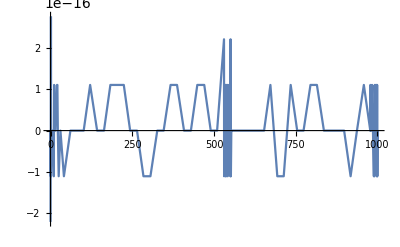

```mathematica
Plot[DiffPolly[r],{r,0,1000}]
```

### Reduction for t Function

```mathematica
FullSimplify[PolynomialQuotient[(r^2+a^2)(ϵ(r^2+a^2)-a*L),(r-RP)(r-RM),r]];
ReducTr =-a L+2 a^2 ϵ+(r^2+RM^2+RM RP+RP^2+r (RM+RP)) ϵ + ((RM^2+a^2)(ϵ(RM^2+a^2)-a*L))/((RM-RP)(r-RM))+ ((RP^2+a^2)(ϵ(RP^2+a^2)-a*L))/((RP-RM)(r-RP));
```

```mathematica
FullSimplify[Together[-a L+2 a^2 ϵ+(r^2+RM^2+RM RP+RP^2+r (RM+RP)) ϵ + ((RM^2+a^2)(ϵ(RM^2+a^2)-a*L))/((RM-RP)(r-RM))+ ((RP^2+a^2)(ϵ(RP^2+a^2)-a*L))/((RP-RM)(r-RP))]]
```

((a^2+r^2) (-a L+(a^2+r^2) ϵ))/((r-RM) (r-RP))

## Int[1/y] Solution

```mathematica
ONEOYHOLO[r_] = 1/Sqrt[J A B] EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2];
```

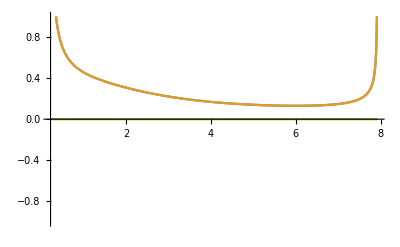

```mathematica
ONEOYHOLO[r_] = 1/Sqrt[J A B] EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2];

Plot[{ONEOYHOLO'[r], 1/Sqrt[RPoly1[r]],ONEOYHOLO'[r]-1/Sqrt[RPoly1[r]]},{r,b,e},PlotRange->{{b,e},{-1,1}}]
```

## Radial Equation

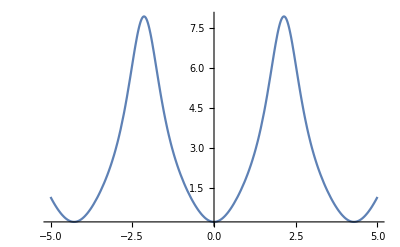

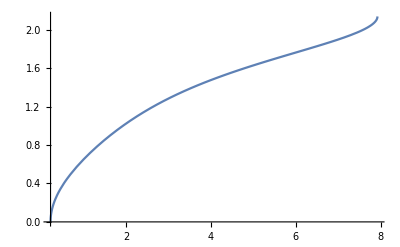

```mathematica
MINO[r_]:=1/Sqrt[J A B] EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2];
r[λ_]:= ((A-B) (A b-B e) SNR[λ]^2+2 (A B (b+e)+A B (b-e) CNR[λ]))/(4 A B+(A-B)^2 SNR[λ]^2);
Plot[r[λ],{λ,-5,5},PlotRange->All]
Plot[MINO[r],{r,b,e}]
```

## Int[r/y] Solution

```mathematica
(*Clear[a,ϵ,L,RM,RP,A,B,b,e,c,d,KZ2,J,r,f,p2,λ,rSub,rSUB,p2]*)
```

### Getting the Eqution

```mathematica
xSUB[r_] := (2Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b))
xSUB[0.6`50]

Sqrt[((e-b)^2-(A-B)^2)/(4*A*B)]
```

0.93836940231259284188235704630718718713913654192

0.025447972209001525726324387171491565793019446383

#### Do integrals by expansion

```mathematica
rSub[λ_] := (p2 λ^2+2(e+b)A*B-2(e-b)A*B*Sqrt[1-λ^2])/((A-B)^2 λ^2+4*A*B);
rSUB[X_] := 1/(A-B)^2(p2 + (2(e+b)A B - p2 f)/(X^2+f) - (2(e-b)A B Sqrt[1-X^2])/(X^2+f));
```

#### Integrals I need

```mathematica
(*Integrate[1/(A-B)^2(p2 + (2(e+b)A B - p2 f)/(x^2+f) - (2(e-b)A B Sqrt[1-x^2])/(x^2+f))(1/(Sqrt[J A B]Sqrt[(1-x^2)(1-KZ2 x^2)])),x]
Integrate[1/(A-B)^2(p2 + (2(e+b)A B - p2 f)/(x^2+f) + (2(e-b)A B Sqrt[1-x^2])/(x^2+f))(1/(Sqrt[J A B]Sqrt[(1-x^2)(1-KZ2 x^2)])),x]
ROYx1[x_]:=(2 A B (b-e) √f ArcTan[(√(1+f KZ2) x)/(√f √(1-KZ2 x^2))]+f √(1+f KZ2) p2 EllipticF[( ArcSin[x]),KZ2]-√(1+f KZ2) (-2 A B (b+e)+f p2) EllipticPi[-1/f,(ArcSin[x]),KZ2])/((A-B)^2 f √(A B J) √(1+f KZ2))
ROYx2[x_]:=(2 A B (b-e) √f ArcTan[(√(1+f KZ2) x)/(√f √(1-KZ2 x^2))]+f √(1+f KZ2) p2 EllipticF[-ArcSin[x],KZ2]-√(1+f KZ2) (-2 A B (b+e)+f p2) EllipticPi[-1/f,-ArcSin[x],KZ2])/((A-B)^2 f √(A B J) √(1+f KZ2))*)
```

### The R Equation

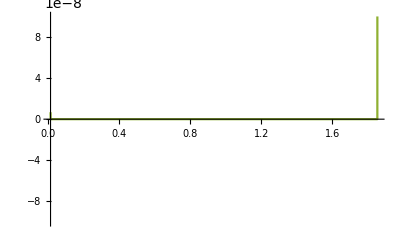

```mathematica
RINT[r_] := 1/((A-B)^2 f √(A B J) √(1+f k^2))(2 A B (b-e) √f ArcTan[(√(1+f k^2) xSUB[r])/(√f √(1-k^2 (xSUB[r])^2))]+f √(1+f k^2) p2 EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]-√(1+f k^2) (-2 A B (b+e)+f p2) EllipticPi[-1/f,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])
Plot[{RINT'[r], r/Sqrt[RPoly1[r]],RINT'[r]-r/Sqrt[RPoly1[r]]},{r,b,e},PlotRange->{{b,e},{-0.0000001,0.0000001}}]
```

### The λ Equation

General::prng: Value of option PlotRange -> PlotRange→{{0,2},{-0.00001,0.00001}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

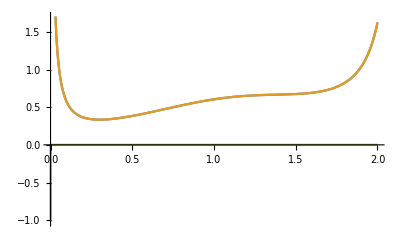

```mathematica
RINTλ[λ_] := ((A b-B e)/(A-B) λ-1/(√J) ArcTan[(e-b)/(2 √(A B))SNR[λ]/Sqrt[1-k^2(SNR[λ])^2]]+((A+B) (e-b))/(2 (A-B) √(A B J)) EllipticPi[-1/f,AMR[λ],k^2])
Plot[{RINTλ'[λ]MINO'[r[λ]], r[λ]/Sqrt[RPoly1[r[λ]]],RINTλ'[λ]MINO'[r[λ]]-r[λ]/Sqrt[RPoly1[r[λ]]]},{λ,0,2},PlotRange-> PlotRange->{{0,2},{-0.00001,0.00001}}]
```

## Int[r^2/y] Solution

### Getting the Equation

```mathematica
r^2 = (8 A^2 B^2 (b^2+e^2)+4 A B (-A B (b-e)^2+(b+e) p2) λ^2+p2^2 λ^4)/((4 A B+(A-B)^2 λ^2)^2) + (4 A B (b-e) √(1-λ^2) (2 A B (b+e)+p2 λ^2))/((4 A B+(A-B)^2 λ^2)^2)
```

Set::write: Tag Power in r^2 is Protected.

```mathematica
FullSimplify[Integrate[1/(Sqrt[1-t^2]Sqrt[1-k^2 t^2]),t]]
```

EllipticF[ArcSin[t],k^2]

```mathematica
FullSimplify[Integrate[1/((t^2+f)^2 Sqrt[1-t^2]Sqrt[1-k^2 t^2]),t]]
```

1/(2 f^2 (1+f) √(-k^2) (1+f k^2) (f+t^2))(f √(-k^2) t √(1-t^2) √(1-k^2 t^2)+ⅈ (f+t^2) (f k^2 (-EllipticE[ⅈ ArcSinh[√(-k^2) t],1/k^2]+(1+f) EllipticF[ⅈ ArcSinh[√(-k^2) t],1/k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),ⅈ ArcSinh[√(-k^2) t],1/k^2]))

```mathematica
1/(2 f^2 (1+f) k (1+f k^2) (f+t^2))(f k t √(1-t^2) √(1-k^2 t^2)+(f+t^2) (f k^2 (-EllipticE[- ArcSin[k t],1/k^2]+(1+f) EllipticF[- ArcSin[k t],1/k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),- ArcSin[k t],1/k^2]))
```

```mathematica
FullSimplify[Integrate[1/((t^2+f)Sqrt[1-t^2]Sqrt[1-k^2 t^2]),t]]
```

EllipticPi[-1/f,ArcSin[t],k^2]/f

```mathematica
FullSimplify[Integrate[1/((t^2+f)Sqrt[1-k^2 t^2]),t]]
```

(k ArcCoth[(√f k √(1+f k^2))/(f k^2+t (k^2 t+√(-k^2) √(1-k^2 t^2)))])/(√f √(-k^2) √(1+f k^2))

```mathematica
FullSimplify[Integrate[1/((t^2+f)^2 Sqrt[1-k^2 t^2]),t]]
```

((√f t √(1-k^2 t^2))/((1+f k^2) (f+t^2))+((k+2 f k^3) ArcCoth[(√f k √(1+f k^2))/(f k^2+t (k^2 t+√(-k^2) √(1-k^2 t^2)))])/(√(-k^2) (1+f k^2)^(3/2)))/(2 f^(3/2))

```mathematica
Setting Up Constants
```

```mathematica
Þ = Evaluate[4A B( p2(b+e) -A B (b-e)^2)];
ð = Evaluate[8 A^2 B^2(b^2+e^2)];
χ = Evaluate[8 A^2 B^2(b^2-e^2)] ;
ψ = Evaluate[4 A B (b-e) p2];

OPP[r_] := 2 Sqrt[A B]Sqrt[(e-r)(r-b)]
ADJ[r_] :=  B(e-r)-A(r-b)
HYP[r_] := B(e-r)+A(r-b)

r2Exact[λ_] :=1/(A-B)^4( (8 A^2 B^2 (b^2+e^2)+4 A B (-A B (b-e)^2+(b+e) p2) λ^2+p2^2 λ^4)/((f+ λ^2)^2)+(4 A B (b-e) √(1-λ^2) (2 A B (b+e)+p2 λ^2))/((f+λ^2)^2));
r2DecompS[s_] :=1/(A-B)^4( p2^2+(Þ-2 f p2^2)/(s+f) + (ð+(f^2 p2^2-Þ f))/(s+f)^2+ (ψ/(f+s)+ (χ-f ψ)/(s+f)^2)Sqrt[1-s])

R2OYNSM[r_]:= 1/(Sqrt[J A B](A-B)^4)( p2^2 EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+(Þ-2 f p2^2)EllipticPi[-1/f, (π/2 -ArcTan[(B(e-r)-A(r-b))/OPP[r]]),k^2]/f +  (ð+(f^2 p2^2-Þ f))1/(2 f^2 (1+f) k (1+f k^2) (f+(xSUB[r])^2))(f k (xSUB[r]) √(1-(xSUB[r])^2) √(1-k^2 (xSUB[r])^2)+(f+(xSUB[r])^2) (f k^2 (-EllipticE[- ArcSin[k(xSUB[r])],1/k^2]+(1+f) EllipticF[- ArcSin[k (xSUB[r])],1/k^2])-(1+2 f+f (2+3 f) k^2) EllipticPi[-1/(f k^2),- ArcSin[k (xSUB[r])],1/k^2]))
+ ψ((k ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(√f √(-k^2) √(1+f k^2)))+ (χ-f ψ)(((√f ( xSUB[r]) √(1-k^2 ( xSUB[r])^2))/((1+f k^2) (f+( xSUB[r])^2))+((k+2 f k^3) ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(I k (1+f k^2)^(3/2)))/(2 f^(3/2))))
```

### The R Equation

```mathematica
R2INT[r_]:= 1/(Sqrt[J A B](A-B)^4)( p2^2 EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+(Þ-2 f p2^2)EllipticPi[-1/f, (π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]/f +  (ð+(f^2 p2^2-Þ f))1/(2 f^2 (1+f) k (1+f k^2) (f+(xSUB[r])^2))(f k (xSUB[r]) ((A (-b+r)+B(-e+r))/(A (b-r)+B (-e+r))) √(1-k^2 (xSUB[r])^2)+(f+(xSUB[r])^2) (f k^2 ((-(EllipticE[-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]- (1-k^2)EllipticF[-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]))/k+(1+f) k EllipticF[-(π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])-(1+2 f+f (2+3 f) k^2)k EllipticPi[-1/f,- (π/2- ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]))
+ ψ((k ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(√f √(-k^2) √(1+f k^2)))+ (χ-f ψ)(((√f ( xSUB[r]) √(1-k^2 ( xSUB[r])^2))/((1+f k^2) (f+( xSUB[r])^2))+((k+2 f k^3) ArcTanh[(f k^2+( xSUB[r]) (k^2 ( xSUB[r])+I k √(1-k^2 ( xSUB[r])^2)))/(√f k √(1+f k^2))])/(I k (1+f k^2)^(3/2)))/(2 f^(3/2))))
```

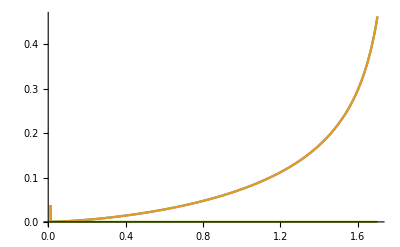

```mathematica
Plot[{Re[R2INT'[r]], r^2/Sqrt[RPoly1[r]],Re[R2INT'[r]-r^2/Sqrt[RPoly1[r]]]},{r,b,e-0.1},PlotRange->All]
```

### The λ Equation

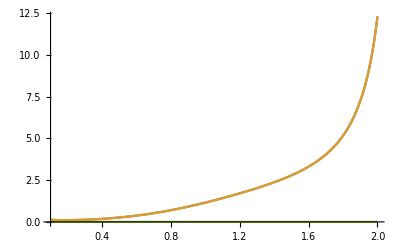

```mathematica
R2INTλ[λ_]:=λ/(A-B)(A b^2-B e^2)+ (√(A B))/(√J)(EllipticE[AMR[λ],k^2])-((A+B) (A^2+2 b^2-B^2-2 e^2))/(4 (A-B) √(A B J))EllipticPi[-1/f,AMR[λ],k^2]-(√(A B) (A+B-(A-B)CNR[λ]))/((A-B) √J)(SNR[λ] DNR[λ])/(f+(SNR[λ])^2)+(A^2+2 b^2-B^2-2 e^2)/(2 (e-b) √J)ArcTan[(k  DNR[λ]SNR[λ] -I k^2( f +   SNR[λ]^2))/(√f k √(1+f k^2))]
Plot[{Re[R2INTλ'[λ]MINO'[r[λ]]], r[λ]^2/Sqrt[RPoly1[r[λ]]],Re[R2INTλ'[λ]MINO'[r[λ]]-r[λ]^2/Sqrt[RPoly1[r[λ]]]]},{λ,0.1,2},PlotRange->All]
```

```mathematica
FullSimplify[√f k √(1+f k^2)]
```

√((A B)/(A-B)^2) √((b-e)^2/(A-B)^2) √(-((A+b-B-e) (A-b-B+e))/(A B))

```mathematica
(ⅈ  √((b-e)^2-(A-B)^2))/(√((b-e)^2))
```

```mathematica
f = (4 A B)/(A-B)^2;
```

```mathematica
p2 = b*A^2+e*B^2-(e+b)*A*B;
```

```mathematica
k = Sqrt[((e-b)^2-(A-B)^2)/(4*A*B)];
```

```mathematica
FullSimplify[Expand[(-b+e) (A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP)))]]
```

-((b-e) (A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP))))

```mathematica
(ⅈ √(A B)√(e-b))/(√J √(A B (b-RP) (eRP)) √(A^2 (b-RP)+(e-RP) (b^2-B^2+e RP-b (e+RP))))
```

## Int[1/((x-RM/RP)y)] Solution

### Getting Equations

```mathematica
((λ^2+f)/(ϛ λ^2+ϡ-RM λ^2-2ϟ Sqrt[1-λ^2]))(1/(Sqrt[1-λ^2]Sqrt[1-k^2 λ^2]));
```

```mathematica
Expand[(ϛ λ^2+ϡ-RM λ^2-2ϟ Sqrt[1-λ^2] )()]
```

1-t^2-k^2 t^2+k^2 t^4

```mathematica
(((A-B)^2 λ^2+4*A*B)/(p2 λ^2+2(e+b)A*B-4*A*B RM-RM(A-B)^2 λ^2-2(e-b)A*B*Sqrt[1-λ^2]))
```

#### Denominator

```mathematica
Expand[(p2 λ^2+2(e+b)A*B-4*A*B RM-RM(A-B)^2 λ^2-2(e-b)A*B*Sqrt[1-λ^2])(p2 λ^2+2(e+b)A*B-4*A*B RM-RM(A-B)^2 λ^2+2(e-b)A*B*Sqrt[1-λ^2])]
```

16 A^2 b B^2 e-16 A^2 b B^2 RM-16 A^2 B^2 e RM+16 A^2 B^2 RM^2+4 A^2 b^2 B^2 λ^2-8 A^2 b B^2 e λ^2+4 A^2 B^2 e^2 λ^2+4 A b B p2 λ^2+4 A B e p2 λ^2-4 A^3 b B RM λ^2+8 A^2 b B^2 RM λ^2-4 A b B^3 RM λ^2-4 A^3 B e RM λ^2+8 A^2 B^2 e RM λ^2-4 A B^3 e RM λ^2-8 A B p2 RM λ^2+8 A^3 B RM^2 λ^2-16 A^2 B^2 RM^2 λ^2+8 A B^3 RM^2 λ^2+p2^2 λ^4-2 A^2 p2 RM λ^4+4 A B p2 RM λ^4-2 B^2 p2 RM λ^4+A^4 RM^2 λ^4-4 A^3 B RM^2 λ^4+6 A^2 B^2 RM^2 λ^4-4 A B^3 RM^2 λ^4+B^4 RM^2 λ^4

```mathematica
FullSimplify[16 A^2 b B^2 e-16 A^2 b B^2 RM-16 A^2 B^2 e RM+16 A^2 B^2 RM^2+4 A^2 b^2 B^2 λ^2-8 A^2 b B^2 e λ^2+4 A^2 B^2 e^2 λ^2+4 A b B p2 λ^2+4 A B e p2 λ^2-4 A^3 b B RM λ^2+8 A^2 b B^2 RM λ^2-4 A b B^3 RM λ^2-4 A^3 B e RM λ^2+8 A^2 B^2 e RM λ^2-4 A B^3 e RM λ^2-8 A B p2 RM λ^2+8 A^3 B RM^2 λ^2-16 A^2 B^2 RM^2 λ^2+8 A B^3 RM^2 λ^2+p2^2 λ^4-2 A^2 p2 RM λ^4+4 A B p2 RM λ^4-2 B^2 p2 RM λ^4+A^4 RM^2 λ^4-4 A^3 B RM^2 λ^4+6 A^2 B^2 RM^2 λ^4-4 A B^3 RM^2 λ^4+B^4 RM^2 λ^4]
```

16 A^2 B^2 (-b+RM) (-e+RM)+4 A B (A^2 RM (-b-e+2 RM)+(b+e-2 RM) (p2-B^2 RM)+A B ((b-e)^2+2 (b+e) RM-4 RM^2)) λ^2+(p2-(A-B)^2 RM)^2 λ^4

```mathematica
DENOM  =ϡ λ^4+ϛ  λ^2 +ϟ
```

```mathematica
ϡ =(p2-(A-B)^2 RM)^2 ;
ϛ = 4 A B (A^2 RM (-b-e+2 RM)+(b+e-2 RM) (p2-B^2 RM)+A B ((b-e)^2+2 (b+e) RM-4 RM^2));
ϟ =16 A^2 B^2 (-b+RM) (-e+RM);
```

#### Numerator

```mathematica
Expand[((A-B)^2 λ^2+4*A*B)(p2 λ^2+2(e+b)A*B-4*A*B RM-RM(A-B)^2 λ^2+2(e-b)A*B*Sqrt[1-λ^2])]
```

8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RM+2 A^3 b B λ^2-4 A^2 b B^2 λ^2+2 A b B^3 λ^2+2 A^3 B e λ^2-4 A^2 B^2 e λ^2+2 A B^3 e λ^2+4 A B p2 λ^2-8 A^3 B RM λ^2+16 A^2 B^2 RM λ^2-8 A B^3 RM λ^2+A^2 p2 λ^4-2 A B p2 λ^4+B^2 p2 λ^4-A^4 RM λ^4+4 A^3 B RM λ^4-6 A^2 B^2 RM λ^4+4 A B^3 RM λ^4-B^4 RM λ^4-8 A^2 b B^2 √(1-λ^2)+8 A^2 B^2 e √(1-λ^2)-2 A^3 b B λ^2 √(1-λ^2)+4 A^2 b B^2 λ^2 √(1-λ^2)-2 A b B^3 λ^2 √(1-λ^2)+2 A^3 B e λ^2 √(1-λ^2)-4 A^2 B^2 e λ^2 √(1-λ^2)+2 A B^3 e λ^2 √(1-λ^2)

```mathematica
FullSimplify[8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RM+2 A^3 b B λ^2-4 A^2 b B^2 λ^2+2 A b B^3 λ^2+2 A^3 B e λ^2-4 A^2 B^2 e λ^2+2 A B^3 e λ^2+4 A B p2 λ^2-8 A^3 B RM λ^2+16 A^2 B^2 RM λ^2-8 A B^3 RM λ^2+A^2 p2 λ^4-2 A B p2 λ^4+B^2 p2 λ^4-A^4 RM λ^4+4 A^3 B RM λ^4-6 A^2 B^2 RM λ^4+4 A B^3 RM λ^4-B^4 RM λ^4-8 A^2 b B^2 √(1-λ^2)+8 A^2 B^2 e √(1-λ^2)-2 A^3 b B λ^2 √(1-λ^2)+4 A^2 b B^2 λ^2 √(1-λ^2)-2 A b B^3 λ^2 √(1-λ^2)+2 A^3 B e λ^2 √(1-λ^2)-4 A^2 B^2 e λ^2 √(1-λ^2)+2 A B^3 e λ^2 √(1-λ^2)]
```

-((4 A B+(A-B)^2 λ^2) (A^2 RM λ^2+(-p2+B^2 RM) λ^2-2 A B (b+e-b √(1-λ^2)+e √(1-λ^2)+RM (-2+λ^2))))

```mathematica
Collect[-((4 A B+(A-B)^2 λ^2) (A^2 RM λ^2+(-p2+B^2 RM) λ^2-2 A B (b+e-b √(1-dd^2)+e √(1-dd^2)+RM (-2+λ^2)))),λ]
```

8 A^2 b B^2-8 A^2 b B^2 √(1-dd^2)+8 A^2 B^2 e+8 A^2 B^2 √(1-dd^2) e-16 A^2 B^2 RM-(-2 A b (A-B)^2 B+2 A b (A-B)^2 B √(1-dd^2)-2 A (A-B)^2 B e-2 A (A-B)^2 B √(1-dd^2) e+4 A^3 B RM+4 A (A-B)^2 B RM-8 A^2 B^2 RM+4 A B (-p2+B^2 RM)) λ^2-(A^2 (A-B)^2 RM-2 A (A-B)^2 B RM+(A-B)^2 (-p2+B^2 RM)) λ^4

```mathematica
α  Z^4-Z^2 (β+γ √(1-λ^2))+φ+ω √(1-λ^2)
```

```mathematica
-8 A^2 b B^2 √(1-dd^2)+8 A^2 B^2 √(1-dd^2) e
```

```mathematica
α =-(A^2 (A-B)^2 RM-2 A (A-B)^2 B RM+(A-B)^2 (-p2+B^2 RM)) ;
β = -(-2 A b (A-B)^2 B-2 A (A-B)^2 B e+4 A^3 B RM+4 A (A-B)^2 B RM-8 A^2 B^2 RM+4 A B (-p2+B^2 RM));
γ= -(2 A b (A-B)^2 B-2 A (A-B)^2 B  e);
φ = 8 A^2 b B^2+8 A^2 B^2 e-16 A^2 B^2 RM;
ω = -8 A^2 b B^2 +8 A^2 B^2 e;
```

```mathematica
α  λ^4+λ^2 β+φ+(γ λ^2 + ω )√(1-λ^2)
```

83912.948161153240032995282152208332272340135137+1195.07765107289350538968611546261947304304422 λ^2+0.077268270079747240354692673010434948349835122 λ^4+√(1-λ^2) (146928.96728530519634767857324196726332017564005+9.54328006546138789209637384981518447247939908 λ^2)

#### FUll Expression

```mathematica
FULLEQ[λ_]:= (1/((p2 λ^2+2(e+b)A*B-2(e-b)A*B*Sqrt[1-λ^2])/((A-B)^2 λ^2+4*A*B)-RM))
REDEQ[λ_] := (α λ^4+λ^2 β+φ)/(ϡ λ^4+ϛ  λ^2 +ϟ)+((γ λ^2 + ω )√(1-λ^2))/(ϡ λ^4+ϛ  λ^2 +ϟ);
REDEQ2[λ_] := 1/ϡ( α+(λ^2( β-(α ϛ)/ϡ)+(φ-(ϟ α)/ϡ))/((λ^2 -D1^2 )(λ^2 -D2^2))+((γ λ^2 + ω )√(1-λ^2))/((λ^2 -D1^2 )(λ^2 -D2^2)));
FULLEQ[0.6`50]-REDEQ2[0.6`50]
```

0.

#### Integrals we need

```mathematica
Clear[A,B,a,b,e,c,p2,RM,k,f,ϡ ,ϛ ,ϟ,α,β,γ,ω,φ,k,D1,D2]
```

```mathematica
Integrate[λ^2/((λ^2-D1^2)(λ^2-D2^2))1/(Sqrt[1-λ^2]Sqrt[1-k^2 λ^2]),λ]
```

(-EllipticPi[1/D1^2,ArcSin[λ],k^2]+EllipticPi[1/D2^2,ArcSin[λ],k^2])/(D1^2-D2^2)

```mathematica
Integrate[1/((λ^2-D1^2)(λ^2-D2^2))1/(Sqrt[1-λ^2]Sqrt[1-k^2 λ^2]),λ]
```

(-D2^2 EllipticPi[1/D1^2,ArcSin[λ],k^2]+D1^2 EllipticPi[1/D2^2,ArcSin[λ],k^2])/(D1^4 D2^2-D1^2 D2^4)

```mathematica
Integrate[1/((λ^2-D1^2)(λ^2-D2^2))1/Sqrt[1-k^2 λ^2],λ]
```

(√(-k^2) (ArcTanh[(D1^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D1 k √(-1+D1^2 k^2))]/(D1 √(-1+D1^2 k^2))-ArcTanh[(D2^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D2 k √(-1+D2^2 k^2))]/(D2 √(-1+D2^2 k^2))))/((D1^2-D2^2) k)

```mathematica
Integrate[λ^2/((λ^2-D1^2)(λ^2-D2^2))1/Sqrt[1-k^2 λ^2],λ]
```

(k (-D1 √(-1+D1^2 k^2) (-1+D2^2 k^2) ArcTanh[(D1^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D1 k √(-1+D1^2 k^2))]+D2 (-1+D1^2 k^2) √(-1+D2^2 k^2) ArcTanh[(D2^2 k^2-λ (k^2 λ+√(-k^2) √(1-k^2 λ^2)))/(D2 k √(-1+D2^2 k^2))]))/((D1-D2) (D1+D2) √(-k^2) (-1+D1 k) (1+D1 k) (-1+D2 k) (1+D2 k))

PacletInstall::samevers: A paclet named Rubi with the same version number (4.16.1.0) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

/Users/conordyson/Library/Mathematica/Paclets/Repository/Rubi-4.16.1.0

### The R Equations

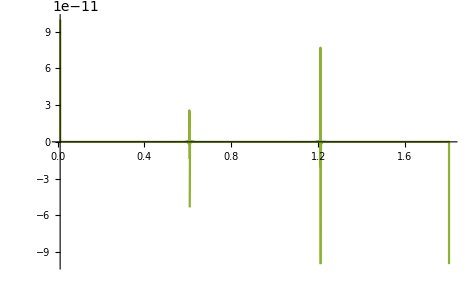

```mathematica
RMINT[r_] := 1/(ϡM Sqrt[J A B]) (αM(EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),KZ2])+( βM-(αM ϛM)/ϡM)(1/(D1M^2-D2M^2)(-EllipticPi[1/D1M^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+EllipticPi[1/D2M^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]))+(φM-(ϟM αM)/ϡM)((-D2M^2 EllipticPi[1/D1M^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+D1M^2 EllipticPi[1/D2M^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])/(D1M^4 D2M^2-D1M^2 D2M^4))+γM ((k (-D1M √(-1+D1M^2 k^2) (-1+D2M^2 k^2) ArcTanh[(D1M^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1M k √(-1+D1M^2 k^2))]+D2M (-1+D1M^2 k^2) √(-1+D2M^2 k^2) ArcTanh[(D2M^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2M k √(-1+D2M^2 k^2))]))/((D1M-D2M) (D1M+D2M) √(-k^2) (-1+D1M k) (1+D1M k) (-1+D2M k) (1+D2M k)))+  ωM (1/((D1M^2-D2M^2) k)√(-k^2) (ArcTanh[(D1M^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1M k √(-1+D1M^2 k^2))]/(D1M √(-1+D1M^2 k^2))-ArcTanh[(D2M^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2M k √(-1+D2M^2 k^2))]/(D2M √(-1+D2M^2 k^2)))));
Plot[{RMINT'[r], 1/((r-RM)Sqrt[RPoly1[r]]),Re[RMINT'[r]-1/((r-RM)Sqrt[RPoly1[r]])]},{r,b,e},PlotRange->{{b,e},{-0.0000000001,0.0000000001}}]
```

```mathematica
RMINT[0.5]
```

-0.416105-0.000781984 ⅈ

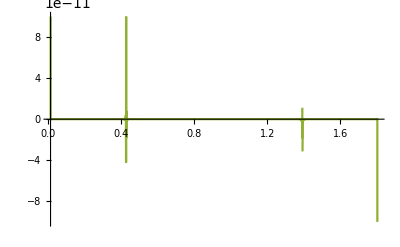

```mathematica
RPINT[r_] := 1/(ϡP Sqrt[J A B]) (αP(EllipticF[(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),KZ2])+( βP-(αP ϛP)/ϡP)((-EllipticPi[1/D1P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+EllipticPi[1/D2P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])/(D1P^2-D2P^2))+(φP-(ϟP αP)/ϡP)((-D2P^2 EllipticPi[1/D1P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2]+D1P^2 EllipticPi[1/D2P^2,(π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]),k^2])/(D1P^4 D2P^2-D1P^2 D2P^4))+γP ((k (-D1P √(-1+D1P^2 k^2) (-1+D2P^2 k^2) ArcTanh[(D1P^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1P k √(-1+D1P^2 k^2))]+D2P (-1+D1P^2 k^2) √(-1+D2P^2 k^2) ArcTanh[(D2P^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2P k √(-1+D2P^2 k^2))]))/((D1P-D2P) (D1P+D2P) √(-k^2) (-1+D1P k) (1+D1P k) (-1+D2P k) (1+D2P k)))+  ωP ((√(-k^2) (ArcTanh[(D1P^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D1P k √(-1+D1P^2 k^2))]/(D1P √(-1+D1P^2 k^2))-ArcTanh[(D2P^2 k^2-(xSUB[r]) (k^2 (xSUB[r])+√(-k^2) √(1-k^2 (xSUB[r])^2)))/(D2P k √(-1+D2P^2 k^2))]/(D2P √(-1+D2P^2 k^2))))/((D1P^2-D2P^2) k)));
Plot[{RPINT'[r], 1/((r-RP)Sqrt[RPoly1[r]]),Re[RPINT'[r]-1/((r-RP)Sqrt[RPoly1[r]])]},{r,b,e},PlotRange->{{b,e},{-0.0000000001,0.0000000001}}]
```

### The λ Equation

```mathematica
RMINTλ[λ_] :=  ((A-B) λ)/(A (b-RM)-B (e-RM))+((e-b) (A (b-RM)+B (e-RM)))/(2 √(A B J) (b-RM) (-e+RM) (A (b-RM)-B (e-RM))) EllipticPi[(A (b-RM)+B (-e+RM))^2/(4 A B (b-RM) (-e+RM)),JacobiAmplitude[√(A B J) λ,k^2],k^2]+(ⅈ A B (e-b))/(√(A B J) √(A B (b-RM) (-e+RM)) √((-b+e) (A^2 (b-RM)+(e-RM) (b^2-B^2+e RM-b (e+RM)))))ArcTanh[(- DNR[λ]SNR[λ]+I k (D2M^2-SNR[λ]^2))/(D2M  √(1-D2M^2 k^2))];


RPINTλ[λ_] := ((A-B) λ)/(A (b-RP)+B (-e+RP))+((e-b) (A (b-RP)+B (e-RP)))/(2 √(A B J) (b-RP) (-e+RP) (A (b-RP)+B (-e+RP))) EllipticPi[1/D2P^2,JacobiAmplitude[√(A B J) λ,k^2],k^2]-Sqrt[(e-b)]/(√J √((RP-b) (e-RP)) √(A^2 (RP-b)-(e-RP) (b^2-B^2+e RP-b (e+RP))))ArcTanh[(DNR[λ]SNR[λ]-I k (D2P^2-SNR[λ]^2))/(D2P  √(1-D2P^2 k^2))]
```

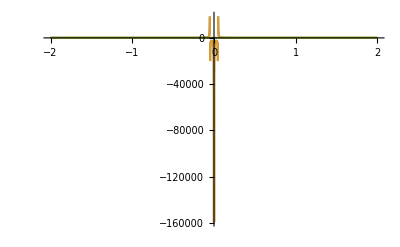

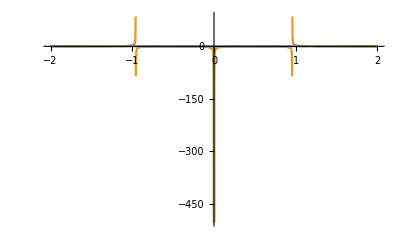

```mathematica
Plot[{RMINTλ'[λ]MINO'[r[λ]], 1/((r[λ]-RM)Sqrt[RPoly1[r[λ]]]),Re[RMINTλ'[λ]MINO'[r[λ]]-1/((r[λ]-RM)Sqrt[RPoly1[r[λ]]])]},{λ,-2,2},PlotRange->All]
Plot[{RPINTλ'[λ]MINO'[r[λ]], 1/((r[λ]-RP)Sqrt[RPoly1[r[λ]]]),Re[RPINTλ'[λ]MINO'[r[λ]]-1/((r[λ]-RP)Sqrt[RPoly1[r[λ]]])]},{λ,-2,2},PlotRange->All]
```

## Polar Equation

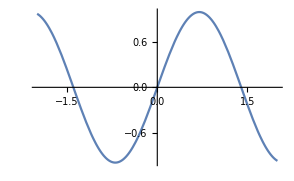

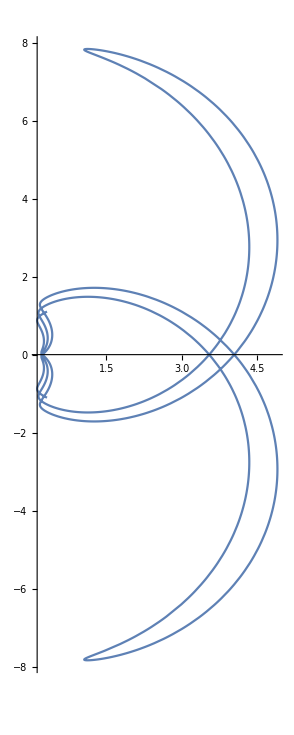

```mathematica
z[λ_] := Z1*JacobiSN[Z2 λ,KZ]  ;
θ[λ_] := ArcCos[Z1*JacobiSN[Z2 λ,KZ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[z[λ],{λ,-2,2}]
ParametricPlot[{Re[r[λ]]*Cos[π/2-Re[θ[λ]]],Re[r[λ]]*Sin[π/2-Re[θ[λ]]]} , {λ,-5,5}, PlotRange->All]
```

## Azimuthal Equation

```mathematica
Integrate[1/(1-z^2)1/Sqrt[(z^2-Z1^2)(a^2 J  z^2-Z2^2)],z]
```

-(ⅈ √(1-z^2/Z1^2) √(1-(a^2 J z^2)/Z2^2) EllipticPi[Z1^2,ⅈ ArcSinh[z √(-1/Z1^2)],(a^2 J Z1^2)/Z2^2])/(√(-1/Z1^2) √((z^2-Z1^2) (a^2 J z^2-Z2^2)))

```mathematica
D[EllipticPi[Z1^2,ArcSin[z 1/Z1],(a^2 J Z1^2)/Z2^2]/Z2,z];
```

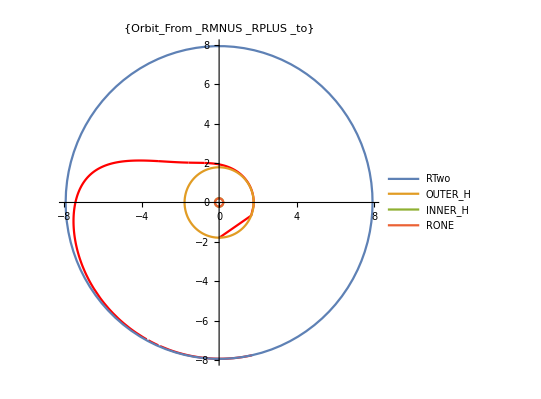

```mathematica
ϕR[λ_]:=a( + (ϵ(RM^2+a^2)-a*L)/(RM-RP)RMINTλ[λ]+ (ϵ(RP^2+a^2)-a*L)/(RP-RM)RPINTλ[λ]);
Subscript[ϕ, z][λ_]:= (L EllipticPi[Z1^2,AMZ[λ],(a^2 J Z1^2)/Z2^2])/Z2
ϕ[λ_]:= ϕR[λ]+Subscript[ϕ, z][λ] 


Q1 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Sin[Re[ϕ[λ]]]}, {λ,MINO[RP],MINO[R2-0.0001]}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{R2*Cos[u],R2 *Sin[u]},
{RP*Cos[u],RP Sin[u]},
{RM*Cos[u],RM Sin[u]},
{R1*Cos[u],R1 Sin[u]}},{u,-π,π},MaxRecursion->1,PlotRange->All,PlotLegends->{RTwo,OUTER_H,INNER_H,RONE}];

Show[Q1,Q2]
```

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,MINO[RP],MINO[R2-0.0001]}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{(RP+0.05)*Sin[u] Sin[v],(RP+0.05)*Cos[u] Sin[v],(RP+0.05)*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[0.1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

## TIME Equation

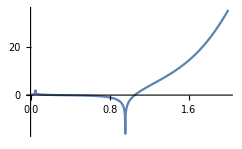

```mathematica
Subscript[T, r][λ_] := ((2 a^2 +RM^2+RM RP+RP^2)ϵ)λ+(R2INTλ[λ]+RINTλ[λ](RM+RP)) ϵ + ((RM^2+a^2)(ϵ(RM^2+a^2)-a*L))/(RM-RP)RMINTλ[λ]+ ((RP^2+a^2)(ϵ(RP^2+a^2)-a*L))/(RP-RM)RPINTλ[λ];
Subscript[T, z][λ_]:=  ϵ/J((Z2-a^2 J/Z2) Z2 λ-Z2 EllipticE[AMZ[λ],KZ]);

T[λ_]:=Subscript[T, r][λ]+Subscript[T, z][λ] 

Plot[{Re@T[λ]},{λ,0,2}]
```

## MINO Time in Terms of Proper Time

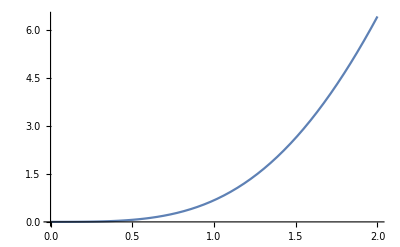

```mathematica
Subscript[τ, r][λ_] := R2INTλ[λ]
Subscript[τ, z][ξ_] :=(Z2(EllipticF[ AMZ[λ],KZ] -  EllipticE[AMZ[λ],KZ]))/J ;
τ[λ_]:= Subscript[τ, z][λ]+Subscript[τ, r][λ]
Plot[Re@τ[λ],{λ,0,2}]
```

## Testing Solutions

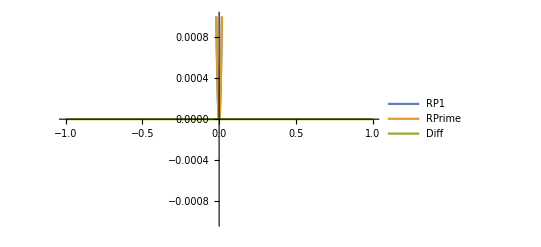

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
Plot[{RPoly1[r[λ]], Re@((r'[λ])^2), Re@((r'[λ])^2)- Re@RPoly1[r[λ]]},{λ,-1,1}, PlotLegends->{RP1,RPrime,Diff}, PlotRange->{{-1,1},{-0.001,0.001}}]
```

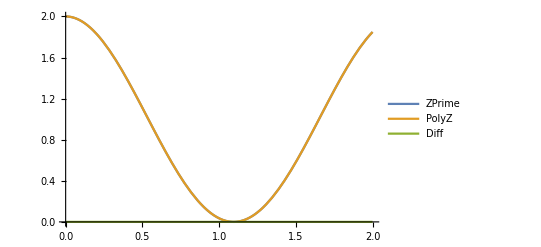

```mathematica
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, PolyZ[λ], (z'[λ])^2- PolyZ[λ]}, {λ,0,2},PlotRange->All, PlotLegends->{ZPrime,PolyZ,Diff}, PlotRange->{{-1,1},{-0.00001,0.00001}}]
```

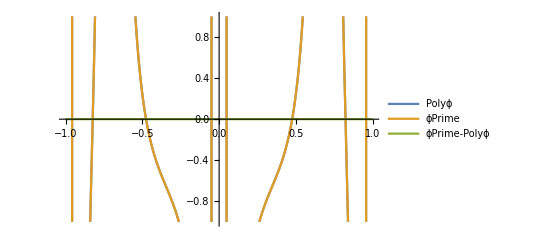

```mathematica
ϕR[λ_]:=a( (ϵ(RM^2+a^2)-a*L)/(RM-RP)RMINTλ[λ]+(ϵ(RP^2+a^2)-a*L)/(RP-RM)RPINTλ[λ]);
ϕ[λ_]:=  ϕR[λ]+Subscript[ϕ, z][λ] 

Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) +L/(1-z[λ]^2)-a ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]]-Re@Polyϕ[λ]},{λ,-1,1}, PlotRange->{{-1,1},{-1,1}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}, PlotRange->{{-1,1},{-0.00000001,0.00000001}}]
```

```mathematica
|
```

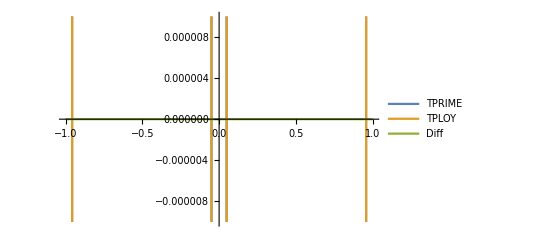

```mathematica
TPoly[λ_]:=((a^2+r[λ]^2) (-a L+(a^2+r[λ]^2) ϵ))/((r[λ]-RM) (r[λ]-RP))- a^2 ϵ (1-z[λ]^2) + a L 
Plot[{Re[T'[λ]],Re@TPoly[λ],Re[T'[λ]]-Re@TPoly[λ] },{λ,-1,1},PlotLegends->{TPRIME,TPLOY,Diff},PlotRange->{{-1,1},{-0.00001,0.00001}}]
```

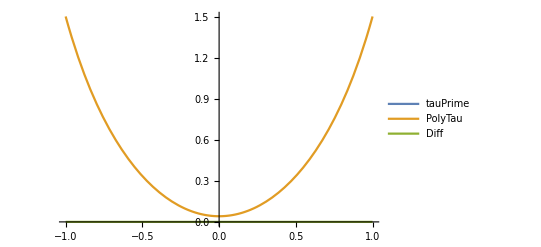

```mathematica
Subscript[τ, r][λ_] := R2INTλ[λ]
Subscript[τ, z][λ_] :=(Z2(EllipticF[ AMZ[λ],KZ] -  EllipticE[AMZ[λ],KZ]))/J ;
τ[λ_]:= Subscript[τ, r][λ]+Subscript[τ, z][λ] 

Plot[{Re@τ'[λ],Re@(r[λ]^2)+ a^2 z[λ]^2,Re@(τ'[λ])-(Re@(r[λ]^2+ a^2 z[λ]^2))},{λ,-1,1},PlotRange->All,{PlotLegends->{tauPrime,PolyTau,Diff}},PlotRange->{{-1,1},{-0.000001,0.000001}}]
```

## Checking Conserved Quantities

### Getting Lower indice equations

```mathematica
Clear["Global`*"]
```

```mathematica
<< GeneralRelativityTensors`
gKR = ToMetric["Kerr"];
TensorValues[gKR]//TableForm;

ModifiedKerr = {{-(1-2 r/(r^2+a^2 z^2)), 0, 0,(-2*a*r(1-z^2))/(r^2+a^2 z^2)}, {0,(r^2+a^2 z^2)/(r^2-2*M*r+a^2),0,0},{0, 0,(r^2+a^2 z^2)/(1-z^2),0} ,{ (-2*a*r(1-z^2))/(r^2+a^2 z^2),0,0,(1-z^2)/(r^2+a^2 z^2)(2*a^2*r(1-z^2)+(a^2+r^2)(r^2+a^2 z^2))}};
ModifiedKerr//MatrixForm;
gMKR = ToMetric[{"NewMetric", "g^MK"}, {t,r,z,ϕ}, ModifiedKerr, "Greek"];
```

```mathematica
U1 = ToTensor[{"NewTensor", "U1"}, gMKR, {(r[λ]^2+a^2 z[λ]^2)^-1 T'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 r'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 z'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 ϕ'[λ]}, {α}];
U2 = ToTensor[{"NewTensor", "U2"}, gMKR, { (r^2+a^2)/(r^2-2M*r+a^2)(ϵ(r^2+a^2)-a*L)-a^2 ϵ(1-z^2)+a*L,-( (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q))^(1/2),(Q-(z^2(a^2(1-ϵ^2)(1-z)^2)+L^2-Q))^(1/2),a/(r^2-2M*r+a^2)(ϵ(r^2+a^2)-a*L) + L/(1-z^2)-a*ϵ}, {α}];
```

```mathematica
U1[-t];
U2[-t];

U1[-ϕ];
U2[-ϕ];
```

### Plots of Conserved Quantities

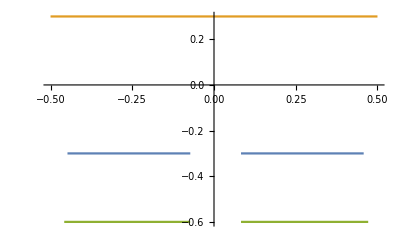

```mathematica
myENERGY[λ_]:= ((-1+(2 r[λ])/(r[λ]^2+a^2 z[λ]^2)) T'[λ])/(r[λ]^2+a^2 z[λ]^2)-(2 a r[λ] (1-z[λ]^2) ϕ'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2))
Plot[{myENERGY[λ],ϵ,myENERGY[λ]-ϵ}, {λ,-0.5,0.5},PlotRange->All]
```

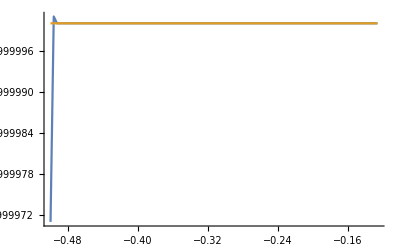

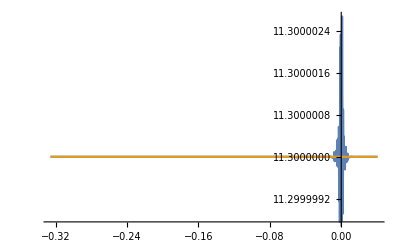

```mathematica
myAngularMomentum[λ_]:= -(2 a r[λ] (1-z[λ]^2) T'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2))+((1-z[λ]^2) (2 a^2 r[λ] (1-z[λ]^2)+(a^2+r[λ]^2) (r[λ]^2+a^2 z[λ]^2)) ϕ'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2));
Plot[{Re[myAngularMomentum[λ]],L}, {λ,-0.5,-MINO[RP]+0.1},PlotRange->All]
Plot[{Re[myAngularMomentum[λ]],L}, {λ,-MINO[RP]-0.1,-MINO[RM]+0.1},PlotRange->All]
```